# Setup

```mathematica
(* ================================================================ *)
(* MODULE 0: SETUP                                                  *)
(* ================================================================ *)

baseDir = NotebookDirectory[];
Get[FileNameJoin[{baseDir, "QKT_full.wl"}]];
$HistoryLength = 0;
EnsureDir[dir_] := If[!DirectoryQ[dir],
  CreateDirectory[dir, CreateIntermediateDirectories -> True]];
kStr[k_] := StringReplace[
  If[StringEndsQ[#, "."], # <> "0", #] &[ToString[N[k]]], "." -> "_"];
```

```mathematica
LaunchKernels[14];
```

# QKT functions used

## Symmetric and non symmetric, comment the floquet operator you want to use

The definition of the sym and non-sym are in the .wl file

```mathematica
Clear[GetQKTParityEigensystem];
GetQKTParityEigensystem[jParam_, alphaParam_, kParam_] :=
  Module[{d=2 jParam + 1,mat, idx, matEven, matOdd, esEven, esOdd,phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,fullVecsEven, fullVecsOdd},
  
(*1. Non symmetric Floquet operator in Jz basis*)
(*mat = Floq[jParam, alphaParam, kParam];*)

(*2. Symmetric Floquet operator in Jz basis*)
mat = Floqsym[jParam, alphaParam, kParam];


    idx = ParitySectorIndices[jParam];
    matEven = mat[[idx["Even"], idx["Even"]]];
    matOdd  = mat[[idx["Odd"], idx["Odd"]]];
    esEven = Eigensystem[matEven, Method -> "Direct"];
    esOdd  = Eigensystem[matOdd, Method -> "Direct"];
    phEven = Mod[Arg[esEven[[1]]], 2 Pi];
    phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];

    idxE = Ordering[phEven];
idxO = Ordering[phOdd];
    vecsEven = esEven[[2, idxE]];
    vecsOdd  = esOdd[[2, idxO]];
    fullVecsEven = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];

    fullVecsOdd = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];

    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
                  "Phases" -> phEven,
                  "Vectors" -> vecsEven,
                  "FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]], 
                  "Phases" -> phOdd,
                  "Vectors" -> vecsOdd,
                  "FullVectors" -> fullVecsOdd|>|>
  ]
```

# Parameters

```mathematica
(* ================================================================ *)
(* MODULE 1: PARAMETERS                                             *)
(* ================================================================ *)

J       = 500;
alpha   = 0.84;
kCenter = 15.;
delta   = 0.01;
nQKT    = 10;
nCOE    = 50;

(* --- Directories --- *)
runLabel = "J" <> ToString[J] <> "_k" <> kStr[kCenter];
resultsDir = FileNameJoin[{baseDir, "Results", runLabel}];
evenDir    = FileNameJoin[{resultsDir, "Even"}];
oddDir     = FileNameJoin[{resultsDir, "Odd"}];
plotDir    = FileNameJoin[{resultsDir, "plots"}];
collageDir = FileNameJoin[{resultsDir, "individual"}];
EnsureDir[evenDir]; EnsureDir[oddDir];
EnsureDir[plotDir]; EnsureDir[collageDir];

(* --- Plot style --- *)
$pOpts = Sequence[ImageSize -> 800, Frame -> True,
  FrameStyle -> Directive[Black, 25],
  LabelStyle -> Directive[Black, 25]];
$cOpts = Sequence[Frame -> True,
  FrameStyle -> Directive[Black, 16],
  LabelStyle -> Directive[Black, 16]];
$cSize = 380;
$legStyle = Directive[Black, 18];

SavePlot[plt_, name_] := (
  Export[FileNameJoin[{plotDir, name <> ".png"}],
    Rasterize[plt, ImageResolution -> 150, Background -> White]];
  Print["  Saved: ", name, ".png"]);
```

# Method

```mathematica
(* --- Generate --- *)
  Print["=== GENERATING QKT ENSEMBLE ==="];
(*  SeedRandom[42];*)
  kList = RandomReal[{kCenter - delta, kCenter + delta}, nQKT];
  {tGen, qktEnsemble} = AbsoluteTiming[
    GenerateQKTEnsemble[J, alpha, kList]];
  Print["  ", nQKT, " matrices done in ", Round[tGen, 0.1], "s"];
  Export[FileNameJoin[{evenDir, "spectra_k"<>ToString[kCenter]<>".wdx"}], qktEnsemble["Even"], "WDX"];
  Export[FileNameJoin[{oddDir, "spectra_k"<>ToString[kCenter]<>".wdx"}], qktEnsemble["Odd"], "WDX"];
  Print["  Spectra exported"];
```

=== GENERATING QKT ENSEMBLE ===

50 matrices done in 72.8s

Spectra exported

```mathematica
(* --- Import --- *)
(*qktEnsemble = <|
    "Even" -> Import[FileNameJoin[{evenDir, "spectra.wdx"}]],
    "Odd"  -> Import[FileNameJoin[{oddDir, "spectra.wdx"}]]|>;
  If[FailureQ[qktEnsemble["Even"]] || FailureQ[qktEnsemble["Odd"]],
    Print["ERROR: Import failed. Check paths."]; Abort[]];
  Print["  Imported successfully"];*)
  qktEnsemble = <|
    "Even" -> Import["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\Results\\J500_k27_5\\Even\\spectra_k27.5.wdx"],
    "Odd"  -> Import["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\Results\\J500_k27_5\\Odd\\spectra_k27.5.wdx"]|>;

  If[FailureQ[qktEnsemble["Even"]] || FailureQ[qktEnsemble["Odd"]],
    Print["ERROR: Import failed. Check paths."]; Abort[]];
  Print["  Imported successfully"];
```

Imported successfully

```mathematica
dimE = qktEnsemble["Even"][[1]]["N"];
dimO = qktEnsemble["Odd"][[1]]["N"];
nReal = Length[qktEnsemble["Even"]];
Print["  Even N=", dimE, ", Odd N=", dimO, ", nReal=", nReal];
```

Even N=401, Odd N=400, nReal=50

# SFF

```mathematica
EnsembleSFFFull[spectraList_List,tauMax_Real,nPts_Integer]:=Module[{nMat,taus,specArray,allK},
nMat=Length[spectraList];
taus=N[Range[1,nPts] (tauMax/nPts)];
specArray=Map[#["Spectrum"]&,spectraList];
DistributeDefinitions[CompileSFF,taus,specArray];
allK=ParallelTable[CompileSFF[specArray[[i]],taus],{i,nMat},Method->"CoarsestGrained"];
<|"Tau"->taus,"AllK"->allK,"MeanK"->Mean[allK],"SE"->StandardDeviation[allK]/Sqrt[nMat*1.]|>];
SmoothSFF[kVec_List,tauVec_List,sigmaTau_?NumericQ]:=GaussianFilter[kVec,sigmaTau/(tauVec[[2]]-tauVec[[1]])];
```

## method

```mathematica
tauMaxSFF=3.0;
nPtsSFF=10000;
sigmaSm=0.01;

sffEven=EnsembleSFFFull[qktEnsemble["Even"],tauMaxSFF,nPtsSFF];
sffOdd=EnsembleSFFFull[qktEnsemble["Odd"],tauMaxSFF,nPtsSFF];
sffCOE=EnsembleSFFFull[coeSpectra,tauMaxSFF,nPtsSFF];

tauGrid=sffEven["Tau"];

(*Smooth each realization individually,then take the mean of the smoothed curves*)
kEvenAllSm=Map[SmoothSFF[#,tauGrid,sigmaSm]&,sffEven["AllK"]];
kOddAllSm=Map[SmoothSFF[#,tauGrid,sigmaSm]&,sffOdd["AllK"]];
kCOEAllSm=Map[SmoothSFF[#,tauGrid,sigmaSm]&,sffCOE["AllK"]];

kEvenMeanSm=Mean[kEvenAllSm];
kOddMeanSm=Mean[kOddAllSm];
kCOEMeanSm=Mean[kCOEAllSm];

kCOEAn=Map[COESFFAnalytical,tauGrid];
```

## plotting

```mathematica
(*Pick one representative realization for the "individual" panel*)
iShow=1;

plotIndiv=ListLinePlot[{Transpose[{tauGrid,sffEven["AllK"][[iShow]]}],Transpose[{tauGrid,kEvenAllSm[[iShow]]}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thin,Gray],Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,Dashed,Red]},PlotLegends->{"raw K_i","smoothed K_i","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Single realization (Even sector, i="<>ToString[iShow]<>")",ImageSize->700]
```

```mathematica
plotEnsemble=ListLinePlot[{Transpose[{tauGrid,kEvenMeanSm}],Transpose[{tauGrid,kOddMeanSm}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,RGBColor[0.8,0.3,0.2]],Directive[Thick,RGBColor[0.3,0.6,0.3]],Directive[Thick,Dashed,Red]},PlotLegends->{"Even smoothed mean","Odd smoothed mean","COE","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF, M = 50, J = 500",ImageSize->700,LabelStyle->Directive[Black,20]]
```

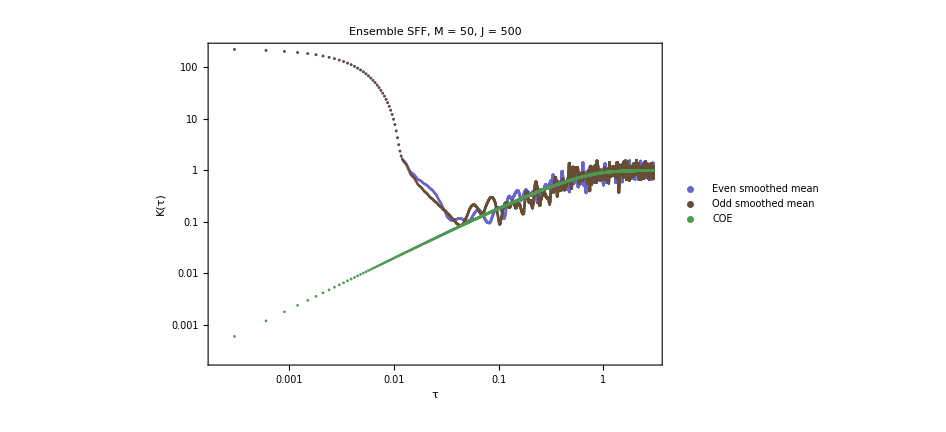

```mathematica
plot400=ListLogLogPlot[{Transpose[{tauGrid,kEvenMeanSm}],Transpose[{tauGrid,kOddMeanSm}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.4,0.4,0.8]],Directive[Thick,RGBColor[0.4,0.3,0.2]],Directive[Thick,RGBColor[0.3,0.6,0.3]],Directive[Thick,Dashed,Red]},PlotLegends->{"Even smoothed mean","Odd smoothed mean","COE","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF, M = 50, J = 500",ImageSize->700,LabelStyle->Directive[Black,20]]
```

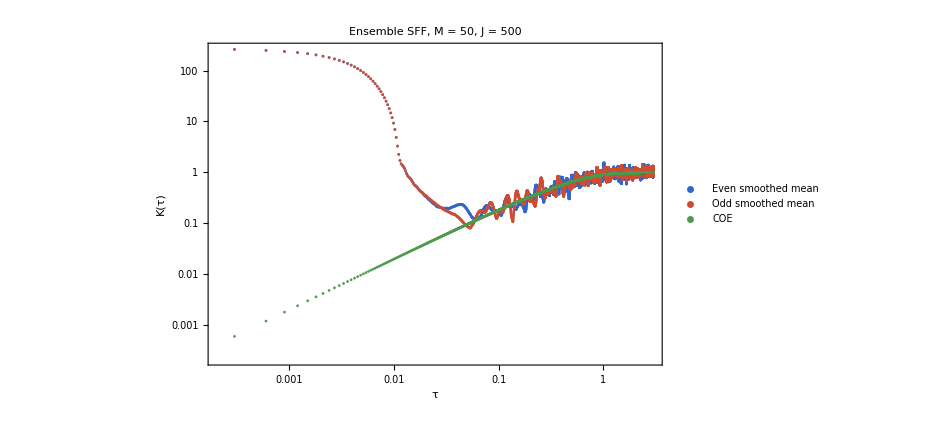

```mathematica
plot500=ListLogLogPlot[{Transpose[{tauGrid,kEvenMeanSm}],Transpose[{tauGrid,kOddMeanSm}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,RGBColor[0.8,0.3,0.2]],Directive[Thick,RGBColor[0.3,0.6,0.3]],Directive[Thick,Dashed,Red]},PlotLegends->{"Even smoothed mean","Odd smoothed mean","COE","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF, M = 50, J = 500",ImageSize->700,LabelStyle->Directive[Black,20]]
```

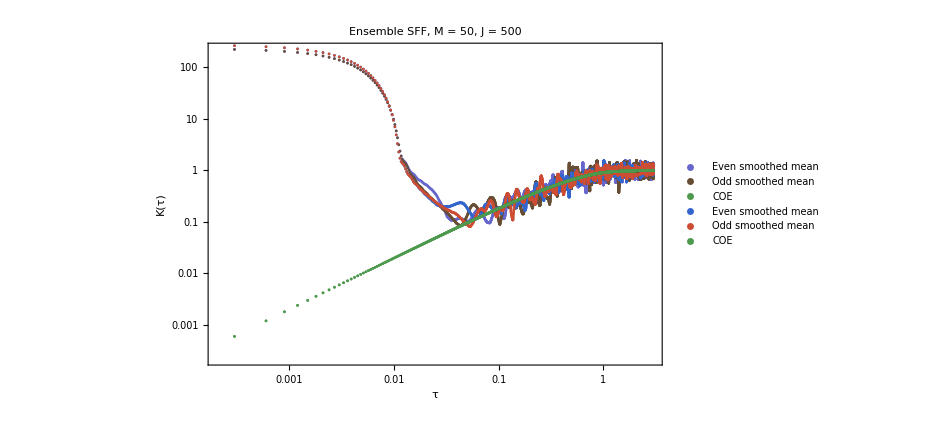

```mathematica
Show[plot400,plot500]
```

# Texture

```mathematica
(*1. DEFINE THE ENSEMBLE FUNCTION*)
Clear[EnsembleTexFull];
EnsembleTexFull[ensembleList_List,tMax_Integer]:=Module[{nMat,tGrid,allTex},
nMat=Length[ensembleList];
tGrid=Range[0,tMax];
Print["Processing ",nMat," realizations up to t = ",tMax,"..."];
DistributeDefinitions[tGrid];

allTex=ParallelTable[
Module[{phases,vecs,d,f1,pArray},
(*Extract data for 1 realization*)
phases=ensembleList[[i,"Phases"]];
vecs=ensembleList[[i,"Vectors"]];

(*Textureless state& Overlaps*)
d=Length[phases];
f1=N@ConstantArray[1/Sqrt[d],d];
pArray=Abs[Conjugate[vecs].f1]^2;
Table[d*Abs[Total[pArray*Exp[-I*t*phases]]]^2,{t,tGrid}]],{i,nMat},Method->"CoarsestGrained"];
(*Return the structured data*)
<|"Time"->tGrid,"AllTex"->allTex,"MeanTex"->Mean[allTex]|>];
```

```mathematica
(*1. Setup Parameters*)
nQKT=50;
J=400;
α=0.84;
kCenter=15.;
(*Adjust your kick perturbation window if needed*)
δ=0.01;
kList=RandomReal[{kCenter-δ,kCenter+δ},nQKT];
```

```mathematica
(*2. Generate all eigensystems in parallel*)
Print["Generating ",nQKT," matrices. This might take a moment..."];
rawEnsembleData=ParallelTable[GetQKTParityEigensystem[J,α,k],{k,kList},Method->"CoarsestGrained"];
```

Generating 50 matrices. This might take a moment...

```mathematica
(*3. Structure the data correctly*)
qktEnsemble=<|"Even"->Table[<|"Phases"->Arg[data["Even","Quasienergies"]],"Vectors"->data["Even","Vectors"]|>,{data,rawEnsembleData}],"Odd"->Table[<|"Phases"->Arg[data["Odd","Quasienergies"]],"Vectors"->data["Odd","Vectors"]|>,{data,rawEnsembleData}]|>;
```

```mathematica
(*4. Ensemble average*)
(*Number of integer kicks to compute*)
tMaxTex=1000;
(*Gaussian smoothing window size in kicks*)
sigmaSm=5;

Print["Computing Even Sector..."];
texEven=EnsembleTexFull[qktEnsemble["Even"],tMaxTex];

Print["Computing Odd Sector..."];
texOdd=EnsembleTexFull[qktEnsemble["Odd"],tMaxTex];

tGrid=texEven["Time"];
```

Computing Even Sector...

Processing 50 realizations up to t = 1000...

Computing Odd Sector...

Processing 50 realizations up to t = 1000...

```mathematica
(*5. Average then smooth*)
texEvenMeanRaw=Mean[texEven["AllTex"]];
texOddMeanRaw=Mean[texOdd["AllTex"]];

texEvenMeanSm=GaussianFilter[texEvenMeanRaw,sigmaSm];
texOddMeanSm=GaussianFilter[texOddMeanRaw,sigmaSm];

(*3. Smooth individual realizations ONLY so Plot 1 doesn't break*)
texEvenAllSm=Map[GaussianFilter[#,sigmaSm]&,texEven["AllTex"]];
texOddAllSm=Map[GaussianFilter[#,sigmaSm]&,texOdd["AllTex"]];
```

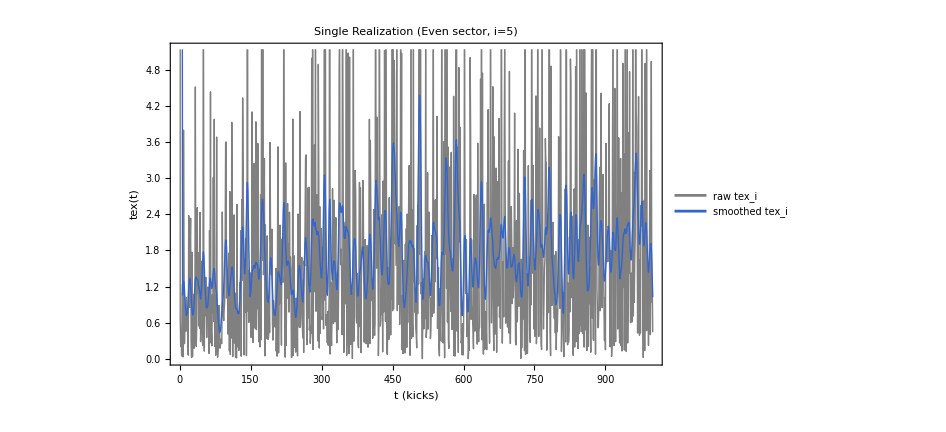

```mathematica
(*---Plot 1:Individual Realization---*)
iShow=5;
plotIndivTex=ListLinePlot[{Transpose[{tGrid,texEven["AllTex"][[iShow]]}],Transpose[{tGrid,texEvenAllSm[[iShow]]}]},PlotStyle->{Directive[Thin,Gray],Directive[Thick,RGBColor[0.2,0.4,0.8]]},PlotLegends->{"raw tex_i","smoothed tex_i"},Frame->True,FrameLabel->{"t (kicks)","tex(t)"},PlotLabel->"Single Realization (Even sector, i="<>ToString[iShow]<>")",ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16]]
```

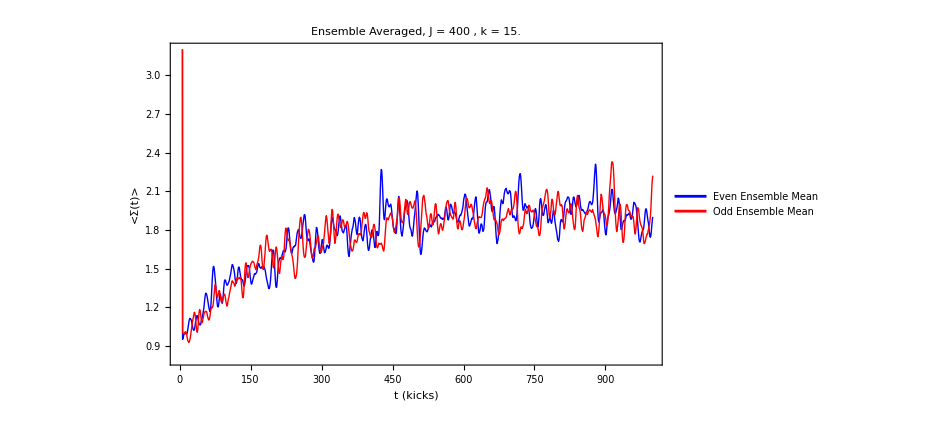

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTex=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Ensemble Averaged, J = "<>ToString[J]<>" , k = "<>ToString[kCenter],ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16],PlotRange->{All,{0.8,3.2}}]
```

```mathematica
Export["texqkt1.png",plotMeanTex,ImageResolution->200]
```

texqkt1.png

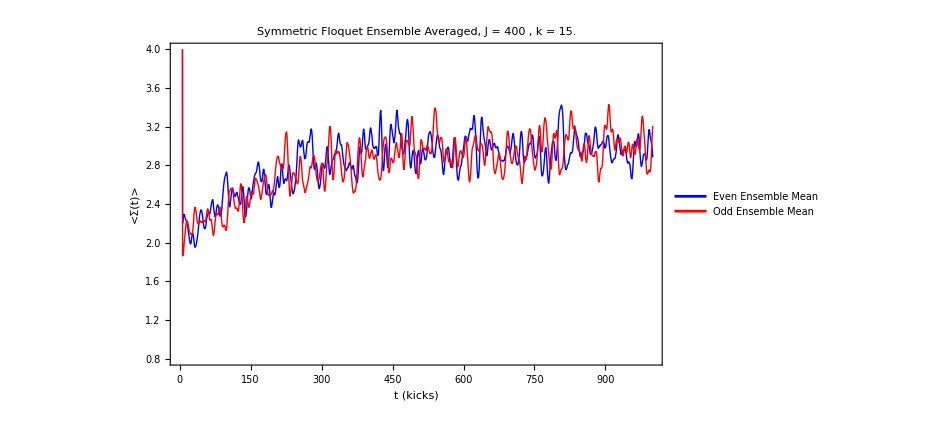

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTexsym=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Symmetric Floquet Ensemble Averaged, J = "<>ToString[J]<>" , k = "<>ToString[kCenter],ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16],PlotRange->{All,{0.8,4}}]
```

```mathematica
Export["texqkt2.png",plotMeanTexsym,ImageResolution->200]
```

texqkt2.png

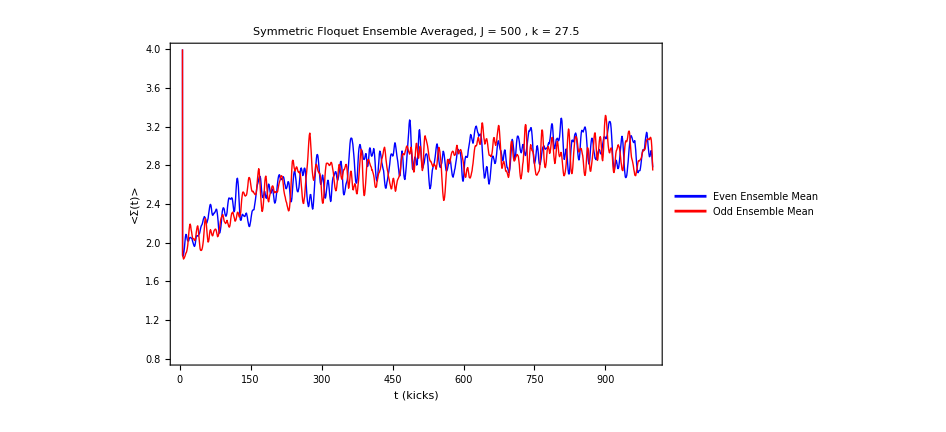

```mathematica
(*---Plot 2:Ensemble Average (Averaging all 20)---*)
plotMeanTex=ListLinePlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Symmetric Floquet Ensemble Averaged, J = "<>ToString[J]<>" , k = "<>ToString[kCenter],ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16],PlotRange->{All,{0.8,4}}]
```

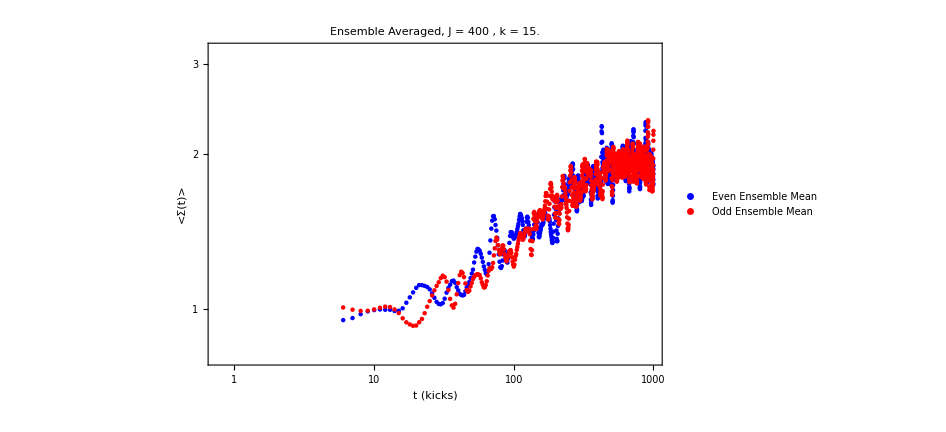

```mathematica
ListLogLogPlot[{Transpose[{tGrid,texEvenMeanSm}],Transpose[{tGrid,texOddMeanSm}]},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotLegends->Placed[LineLegend[{"Even Ensemble Mean","Odd Ensemble Mean"}],{0.85,0.15}],Frame->True,FrameLabel->{"t (kicks)","<Σ(t)>"},PlotLabel->"Ensemble Averaged, J = "<>ToString[J]<>" , k = "<>ToString[kCenter],ImageSize->700,FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16],PlotRange->{All,{0.8,3.2}}]
```

# Entanglement entropy

```mathematica
EntanglementEntropySVD[psi_, dA_, dB_] :=
  Module[{mat, sv2},
    mat = ArrayReshape[psi, {dA, dB}];
    sv2 = SingularValueList[mat]^2;
    (* Hard threshold at machine epsilon level *)
    sv2 = Select[sv2, # > 1.*^-14 &];
    (* Renormalize to absorb discarded numerical noise *)
    sv2 = sv2 / Total[sv2];
    -sv2 . Log[sv2]
  ]
```

```mathematica
(* Build embedding T: maps Dicke |j,m⟩ -> |j1,m1⟩⊗|j2,m2⟩  
   for the maximally-stretched split j1 + j2 = j *)
BuildCGEmbedding[j_,j1_]:=Module[{j2=j-j1,d=2 j+1,d1=2 j1+1,d2,lg,m1V,m2V,cgVals,posList},d2=2 (j-j1)+1;
lg=Table[LogGamma[n+1.],{n,0,2 j}];
m1V=Range[j1,-j1,-1];
m2V=Range[j2,-j2,-1];
cgVals=Flatten@Table[With[{m=m1+m2},Exp[0.5 (lg[[2 j1+1]]+lg[[2 j2+1]]-lg[[2 j+1]]+lg[[j+m+1]]+lg[[j-m+1]]-lg[[j1+m1+1]]-lg[[j1-m1+1]]-lg[[j2+m2+1]]-lg[[j2-m2+1]])]],{m1,m1V},{m2,m2V}];
posList=Flatten[Table[{(j1-m1V[[i]]) d2+(j2-m2V[[k]])+1,j-(m1V[[i]]+m2V[[k]])+1},{i,d1},{k,d2}],1];
SparseArray[Thread[posList->cgVals],{d1 d2,d}]]

(* Entanglement of a Dicke-basis eigenstate after CG embedding *)
QKTEntanglementSVD[psi_, T_, dA_, dB_] := Module[
  {psiTP, mat, sv2},
  psiTP = T . psi;
  mat = ArrayReshape[psiTP, {dA, dB}];
  sv2 = SingularValueList[mat]^2;
  sv2 = Select[sv2, # > 1.*^-14 &];
  sv2 = sv2 / Total[sv2];
  -sv2 . Log[sv2]
]
```

```mathematica
QKTEntanglementFast[psi_, T_, dA_, dB_] := Module[
  {mat, sv2, dmin},
  mat = ArrayReshape[T . psi, {dA, dB}];
  dmin = Min[dA, dB];
  (* Eigenvalues of the smaller Gram matrix -> squared singular values *)
  sv2 = If[dA <= dB,
    Re[Eigenvalues[mat . ConjugateTranspose[mat]]],
    Re[Eigenvalues[ConjugateTranspose[mat] . mat]]
  ];
  sv2 = Select[sv2, # > 1.*^-14 &];
  sv2 = sv2 / Total[sv2];
  -sv2 . Log[sv2]
]
```

```mathematica
J = 500;
j1 = J/2;             (* balanced split; use Floor[J/2] if J is odd *)
j2 = J - j1;
d1 = 2 j1 + 1;
d2 = 2 j2 + 1;

T = BuildCGEmbedding[J, j1];   (* compute once *)
```

```mathematica
data=GetQKTParityEigensystem[J,0.84,15.];
```

```mathematica
evenvecs=data["Even","FullVectors"];
```

```mathematica
oddvecs=data["Odd","FullVectors"];
```

```mathematica
(* Apply to a full-basis eigenvector (length 2J+1) *)
enteven=ParallelTable[QKTEntanglementFast[i, T, d1, d2],{i,evenvecs}];
entodd=ParallelTable[QKTEntanglementFast[i, T, d1, d2],{i,oddvecs}];
```

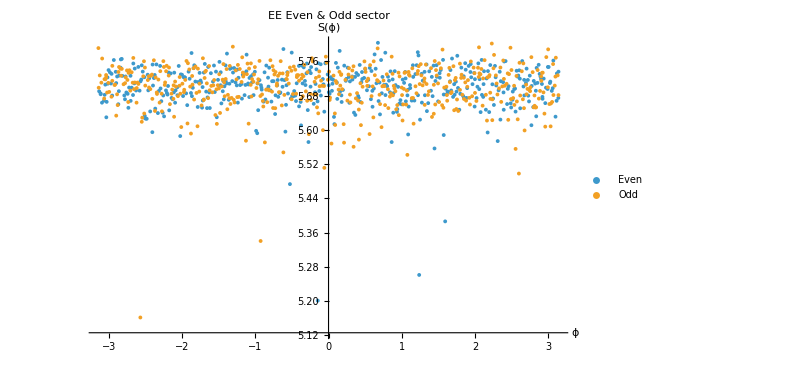

```mathematica
ListPlot[{Transpose[{Arg[data["Even","Quasienergies"]],enteven}],Transpose[{Arg[data["Odd","Quasienergies"]],entodd}]},PlotRange->All,ImageSize->600,PlotLegends->{"Even","Odd"},PlotLabel->Style["EE Even & Odd sector",25,Black],AxesLabel->{Style["ϕ",20,Black],Style["S(ϕ)",20,Black]}]
```

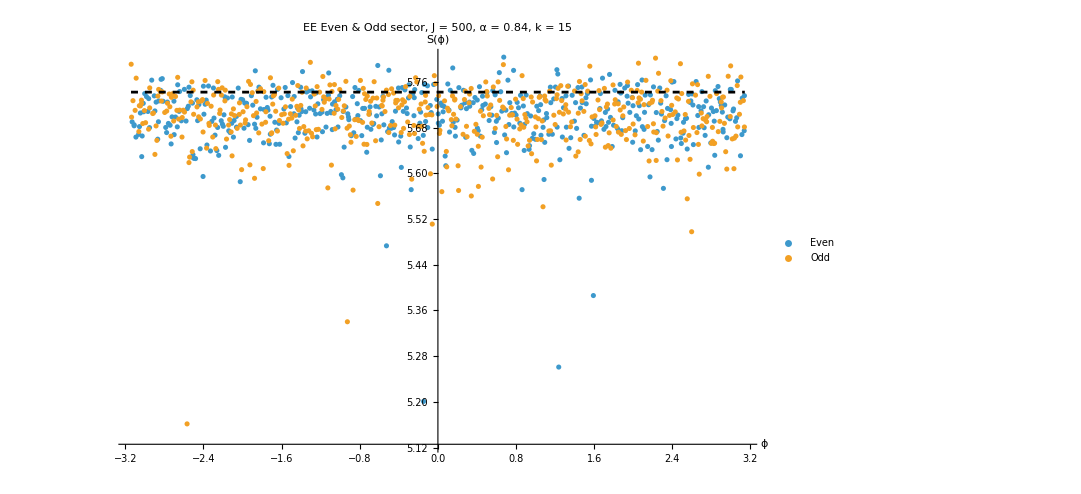

```mathematica
plot=Show[{ListPlot[{Transpose[{Arg[data["Even","Quasienergies"]],enteven}],Transpose[{Arg[data["Odd","Quasienergies"]],entodd}]},PlotRange->All,ImageSize->800,PlotLegends->{"Even","Odd"},PlotLabel->Style["EE Even & Odd sector, J = 500, α = 0.84, k = 15",25,Black],AxesLabel->{Style["ϕ",20,Black],Style["S(ϕ)",20,Black]}],Plot[pageqkt,{x,-Pi,Pi},PlotStyle->{Black,Dashed}]}]
```

```mathematica
Export["EEQKT.png",plot,ImageResolution->300]
```

EEQKT.png

```mathematica
Log[1001.]
```

6.90875

```mathematica
PageQKTNumerical[T_,dA_,dB_,d_,nSamples_]:=Mean[Table[QKTEntanglementFast[Normalize[RandomVariate[NormalDistribution[],d]+I RandomVariate[NormalDistribution[],d]],T,dA,dB],{nSamples}]]
```

```mathematica
pageqkt=PageQKTNumerical[T,d1,d2,2J+1,100];
```

# COE Reference

```mathematica
(* 1. SETUP PARAMETERS FOR COE                                      *)
nMat = 50;    (* Number of realizations / matrices *)
dim = 350;    (* Matrix dimension (Matches J/2 for J=400) *)

Print["Generating ", nMat, " COE matrices of dimension ", dim, "..."];

(* 2. Generate Eigensystems directly from Random Matrix Theory *)
coeEnsembleData = ParallelTable[
  Module[{mat, vals, vecs},
        (* Draw a random symmetric unitary matrix from the COE *)
    mat = RandomVariate[CircularOrthogonalMatrixDistribution[dim]];
        (* Compute the eigensystem *)
    {vals, vecs} = Eigensystem[mat];
        (* Structure it exactly how EnsembleTexFull expects it *)
    <|
      "Phases" -> Arg[vals], 
      "Vectors" -> vecs
    |>
  ],
  {nMat},
  Method -> "CoarsestGrained"
];

Print["Done! Length of COE Ensemble: ", Length[coeEnsembleData]];
```

Generating 50 COE matrices of dimension 350...

Done! Length of COE Ensemble: 50

```mathematica
(* 3. COMPUTE THE ENSEMBLE AVERAGE (COE)*)

tMaxTex = 1000; (* Number of integer kicks to compute *)
sigmaSm = 5;   (* Gaussian smoothing window size in kicks *)

Print["Computing COE Survival Probability..."];
texCOE = EnsembleTexFull[coeEnsembleData, tMaxTex];

tGrid = texCOE["Time"];
```

Computing COE Survival Probability...

Processing 50 realizations up to t = 1000...

```mathematica
(*4. AVERAGE FIRST,THEN SMOOTH (COE)*)
texCOEMeanRaw=Mean[texCOE["AllTex"]];
texCOEMeanSm=GaussianFilter[texCOEMeanRaw,sigmaSm];
texCOEAllSm=Map[GaussianFilter[#,sigmaSm]&,texCOE["AllTex"]];
```

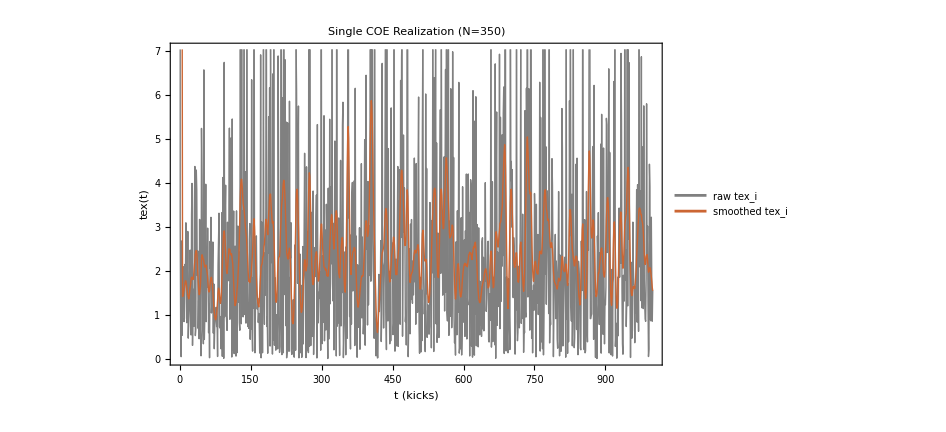

```mathematica
(* --- Plot 1: Individual COE Realization --- *)
iShow = 1;
plotIndivCOE = ListLinePlot[
  {
    Transpose[{tGrid, texCOE["AllTex"][[iShow]]}], 
    Transpose[{tGrid, texCOEAllSm[[iShow]]}]
  },
  PlotStyle -> {
    Directive[Thin, Gray], 
    Directive[Thick, RGBColor[0.8, 0.4, 0.2]] (* Using Orange/Red for COE *)
  },
  PlotLegends -> {"raw tex_i", "smoothed tex_i"},
  Frame -> True, 
  FrameLabel -> {"t (kicks)", "tex(t)"},
  PlotLabel -> "Single COE Realization (N=" <> ToString[dim] <> ")",
  ImageSize -> 700,
  FrameStyle -> Directive[Black, 16],
  LabelStyle -> Directive[Black, 16]
]
```

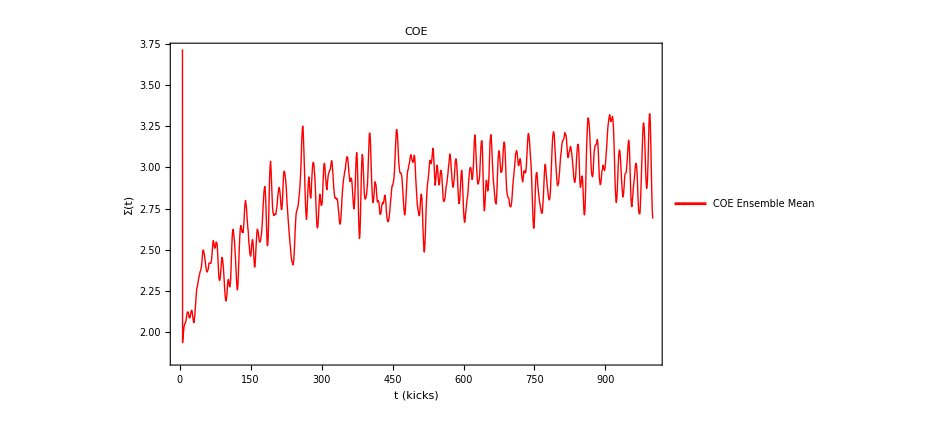

```mathematica
(* --- Plot 2: COE Ensemble Average --- *)
plotMeanCOE = ListLinePlot[
  Transpose[{tGrid, texCOEMeanSm}],
  PlotStyle -> Directive[Thick, Red],
  PlotLegends -> Placed[LineLegend[{"COE Ensemble Mean"}], {0.85, 0.15}],
  Frame -> True,
  FrameLabel -> {"t (kicks)", "Σ(t)"},
  PlotLabel -> "COE",
  ImageSize -> 700,
  FrameStyle -> Directive[Black, 16],
  LabelStyle -> Directive[Black, 16]
]
```

# Tests 1 reality of eigenvectors

```mathematica
Clear[sz,sp,sm,sx,sy,sx2,twistPart,freePart,Floq,Floqsym];

(*1. Basic Operators*)
sz[j_]:=SparseArray[Band[{1,1}]->Range[j,-j,-1]];
sp[j_]:=SparseArray[Band[{1,2}]->Table[Sqrt[j (j+1)-m (m+1)],{m,j-1,-j,-1}],{2 j+1,2 j+1}];
sm[j_]:=SparseArray[Band[{2,1}]->Table[Sqrt[j (j+1)-m (m-1)],{m,j,-j+1,-1}],{2 j+1,2 j+1}];

sx[j_]:=(1/2) (sp[j]+sm[j]);
sy[j_]:=(1/(2 I)) (sp[j]-sm[j]);
sx2[j_]:=sx[j].sx[j];
```

```mathematica
(*3. Floquet Operators (Notice the underscores added to the left side!)*)
twistPart[j_,k_]:=MatrixExp[(-I k/(2 j)) sx2[j]];
freePart[j_,α_]:=SparseArray[Band[{1,1}]->Exp[-I α Range[j,-j,-1]]];
Floq[j_,α_,k_]:=twistPart[j,k].freePart[j,α];
Floqsym[j_,α_,k_]:=freePart[j,α/2].twistPart[j,k].freePart[j,α/2];
```

```mathematica
(*2. Parameters*)
J=3;
α=Pi/4;
k=15.;
```

```mathematica
mat1=Floq[J,α,k];
```

```mathematica
{eval1,evec1}=Eigensystem[mat1];
```

```mathematica
evec1//Im//FullSimplify
```

{{0.323991,-1.02133×10^-16,-0.282685,5.81058×10^-17,0.396979,-6.86874×10^-17,0.},{0.387952,-8.48876×10^-17,0.,-7.26661×10^-18,0.128673,-1.72287×10^-18,-0.125251},{-1.59092×10^-16,0.,-5.37775×10^-15,-0.181127,1.59357×10^-15,0.159477,-6.14497×10^-16},{-4.89571×10^-16,-0.138446,-3.67785×10^-17,0.,-9.98635×10^-16,-0.225548,2.87909×10^-16},{3.70628×10^-17,0.229592,1.97928×10^-17,-0.192956,-7.65536×10^-17,0.,-1.02732×10^-16},{-0.393279,1.00273×10^-16,0.195736,1.13588×10^-17,-0.205738,1.02201×10^-18,0.},{-0.423921,-9.48524×10^-17,0.340287,-9.28222×10^-17,0.,-9.2538×10^-18,0.104054}}

```mathematica
(*4. Evaluate the Matrix*)
mat2=Floqsym[J,α,k];
```

```mathematica
{eval2,evec2}=Eigensystem[mat2];
```

```mathematica
evec2//Im//Chop
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

# Tests 2 gauge transformation F_sym

```mathematica
J=400;
alpha=0.84;
k=15;
```

```mathematica
satGauge[theta_]:=Module[{D,U,V,P,idx,Vsec},D=DiagonalMatrix[Exp[I theta Range[J,-J,-1]]];
U=D.Floqsym[J,alpha,k].ConjugateTranspose[D];
idx=ParitySectorIndices[J]["Even"];
V=Eigenvectors[U[[idx,idx]]];
P=Abs[V.ConstantArray[1/Sqrt[Length[idx]],Length[idx]]]^2;
Length[idx]*Total[P^2]];
```

```mathematica
DistributeDefinitions[satGauge,Floqsym];
```

```mathematica
data=ParallelTable[{theta,satGauge[theta]},{theta,0,alpha/2,alpha/40},DistributedContexts->Full];
```

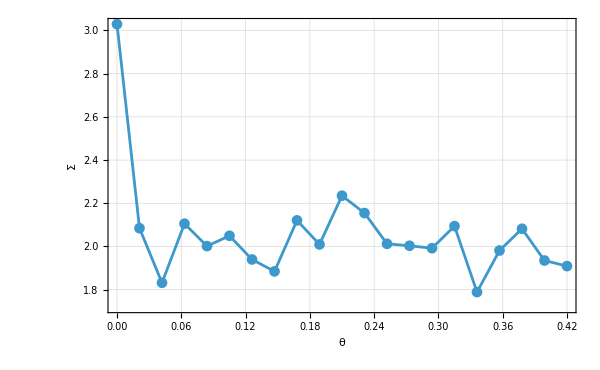

```mathematica
ListPlot[data,Joined->True,PlotMarkers->Automatic,PlotTheme->"Detailed",FrameLabel->{"θ","Σ"},LabelStyle->Directive[Black, 20],ImageSize->600,PlotRange->All]
```

## by sectors

```mathematica
J = 300;
alpha = 0.84;
k = 15;
```

```mathematica
satGauge[theta_] := Module[
  {D, U, idxE, idxO, dE, dO, VE, VO, f1E, f1O, PE, PO, satE, satO},
  
  D = DiagonalMatrix[Exp[I theta Range[J, -J, -1]]];
  U = D . Floqsym[J, alpha, k] . ConjugateTranspose[D];
  
  idxE = ParitySectorIndices[J]["Even"];
  idxO = ParitySectorIndices[J]["Odd"];
  dE = Length[idxE];
  dO = Length[idxO];
  
  VE = Eigenvectors[U[[idxE, idxE]]];
  VO = Eigenvectors[U[[idxO, idxO]]];
  
  f1E = ConstantArray[1/Sqrt[dE], dE];
  f1O = ConstantArray[1/Sqrt[dO], dO];
  
  PE = Abs[VE . f1E]^2;
  PO = Abs[VO . f1O]^2;
  
  satE = dE * Total[PE^2];
  satO = dO * Total[PO^2];
  
  {satE, satO}
];
```

```mathematica
DistributeDefinitions[satGauge, Floqsym, ParitySectorIndices,Floq, J, alpha, k];
```

```mathematica
Range[-alpha/2, alpha/2, alpha/50]
```

{-0.42,-0.4032,-0.3864,-0.3696,-0.3528,-0.336,-0.3192,-0.3024,-0.2856,-0.2688,-0.252,-0.2352,-0.2184,-0.2016,-0.1848,-0.168,-0.1512,-0.1344,-0.1176,-0.1008,-0.084,-0.0672,-0.0504,-0.0336,-0.0168,0.,0.0168,0.0336,0.0504,0.0672,0.084,0.1008,0.1176,0.1344,0.1512,0.168,0.1848,0.2016,0.2184,0.2352,0.252,0.2688,0.2856,0.3024,0.3192,0.336,0.3528,0.3696,0.3864,0.4032,0.42}

```mathematica
rawData = ParallelTable[
  {theta, satGauge[theta]},
  {theta, -alpha/2, alpha/2, alpha/100},
  DistributedContexts -> Full
];
```

```mathematica
dataEven = {#[[1]], #[[2, 1]]} & /@ rawData;
dataOdd  = {#[[1]], #[[2, 2]]} & /@ rawData;
```

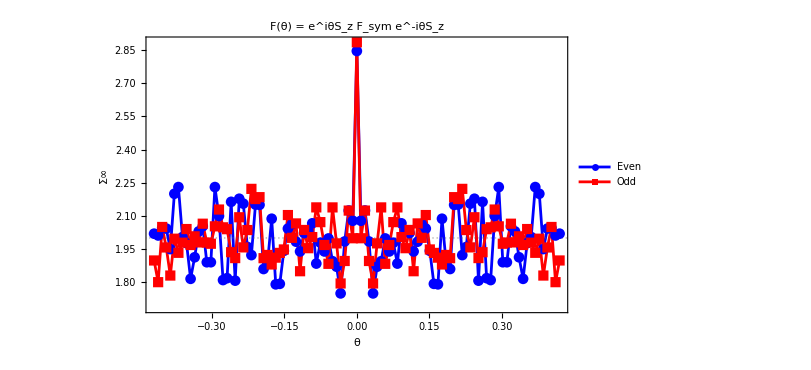

```mathematica
ListPlot[
 {dataEven, dataOdd},
 Joined -> True,
 PlotMarkers -> Automatic,
 PlotTheme -> "Detailed",
 FrameLabel -> {
   "θ",
   "Σ∞"
 },
 PlotLabel -> Style[
   Row[{
     "F(θ) = e", Superscript["", "iθ\!\(\*SubscriptBox[\(S\), \(z\)]\)"],
     " \!\(\*SubscriptBox[\(F\), \(sym\)]\) e", 
     Superscript["", "-iθ\!\(\*SubscriptBox[\(S\), \(z\)]\)"]
   }], 18, Black
 ],
 LabelStyle -> Directive[Black, 20],
 ImageSize -> 600,
 PlotRange -> All,
 PlotLegends -> {"Even", "Odd"},
 GridLines -> {None, {2, 3}},
 PlotStyle -> {Blue, Red}
]
```

# Ising

## Paquetes y funciones

```mathematica
Get["C:\\Users\\Miguel\\Github\\libs\\QMB\\Kernel\\init.m"];
```

Pauli::shdw: Symbol Pauli appears in multiple contexts {QMB`,Global`}; definitions in context QMB` may shadow or be shadowed by other definitions.

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

IsingHamiltonian::shdw: Symbol IsingHamiltonian appears in multiple contexts {QMB`ManyBody`,Global`}; definitions in context QMB`ManyBody` may shadow or be shadowed by other definitions.

Get::noopen: Cannot open C:\Users\Miguel\Github\libs\QMB\ManyBody\Fermions.wl.

```mathematica
TexturelessState[d_] := TexturelessState[d] = N@ConstantArray[1/Sqrt[d], d]
```

```mathematica
QuantumTexture[Hamiltonian_?MatrixQ] := Module[
  {
      dim = Length[Hamiltonian],
      evals,
      evecs,
      Pk,
      f1
  },
  
  f1 = TexturelessState[dim];
  
  (* 1. Single diagonalization (O(d^3)) *)
  {evals, evecs} = Eigensystem[N[Hamiltonian]];
    
  (* 2. Cálculo de los pesos P_k = |<E_k | psi_0>|^2 (O(d^2)) *)
  Pk = Abs[Conjugate[evecs] . f1]^2;
    
  (* 3. Retornamos una función pura vectorizada para evaluación en O(d) *)
  Function[TimeArgument,
    Module[{TimeList, PhaseMatrix, SurvivalAmplitudes},
        TimeList = Flatten[{TimeArgument}];
          
        (* Outer product para vectorizar el cálculo de fases e^{-i E_k t} *)
        PhaseMatrix = Outer[Times, TimeList, evals];
            
        (* Producto punto para sumar amplitudes *)
        SurvivalAmplitudes = Exp[-I * PhaseMatrix].Pk;
          
        (* Textura según la Ec. 12 y 13: d * |A(t)|^2 *)
        dim * Abs[SurvivalAmplitudes]^2
    ]
  ]
]
```

```mathematica
(* Defines el estilo base una sola vez *)
sharedPlotOptions = Sequence[
    Frame->True,
ImageSize->700,ImagePadding->All,FrameTicksStyle->Directive[Black,FontFamily->"Source Sans Pro",FontSize->Scaled[0.03]],
FrameStyle->Directive[Black,FontFamily->"Source Sans Pro",FontSize->Scaled[0.03]]
];
```

```mathematica
(* Overloaded Energy-Window Version *)
QuantumTexture[HamiltonianMatrix_?MatrixQ, {EnergyMin_?NumericQ, EnergyMax_?NumericQ}] := Module[
    {
        FullDimension,
        EigenValues,
        EigenVectors,
        InitialState,
        AllProbabilities,
        FilteredIndices,
        FilteredEvals,
        FilteredPk,
        EffectiveDimension
    },
    
    FullDimension = Length[HamiltonianMatrix];
    
    (* 1. Diagonalization *)
    {EigenValues, EigenVectors} = Eigensystem[N[HamiltonianMatrix]];
    
    (* 2. Find indices within the window *)
    FilteredIndices = Flatten[Position[EigenValues, e_ /; EnergyMin <= e <= EnergyMax]];
    
    (* 3. Filter data and define Effective Dimension *)
    FilteredEvals = EigenValues[[FilteredIndices]];
    EffectiveDimension = Length[FilteredIndices];
    InitialState = Join[TexturelessState[EffectiveDimension],ConstantArray[0,FullDimension-EffectiveDimension]];
    
    (* Calculate Pk only for the relevant eigenvectors *)
    FilteredPk = Normalize[Abs[Conjugate[EigenVectors[[FilteredIndices]]] . InitialState]^2, Total];
    
    (* 4. Optimized temporal function *)
    Function[TimeArgument,
        Module[{TimeList, PhaseMatrix, SurvivalAmplitudes},
            TimeList = Flatten[{TimeArgument}];
            
            (* Vectorized phase calculation *)
            PhaseMatrix = Outer[Times, TimeList, FilteredEvals];
            SurvivalAmplitudes = Exp[-I * PhaseMatrix] . FilteredPk;
            
            (* Scaling by Effective Dimension as requested *)
            If[Length[TimeList] == 1,
                EffectiveDimension * Abs[SurvivalAmplitudes[[1]]]^2,
                EffectiveDimension * Abs[SurvivalAmplitudes]^2
            ]
        ]
    ]
]
```

### Prueba QuantumTexture

```mathematica
d=100;
dim=500;
tList=Range[0,d,0.5];

ensembleSize=50;

texturesEnsemble=Table[
texture=QuantumTexture[RandomVariate[GaussianOrthogonalMatrixDistribution[dim]]];texture[tList]
,ensembleSize];
```

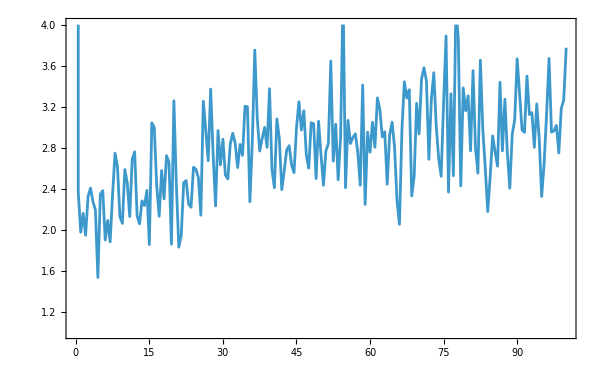

```mathematica
ListPlot[Transpose[{tList,Mean[texturesEnsemble]}],
PlotRange->{All,{1,4}},
Joined->True,
Frame->True,
ImageSize->600,ImagePadding->All,FrameTicksStyle->Directive[Black,FontFamily->"Source Sans Pro",FontSize->Scaled[0.03]],
FrameStyle->Directive[Black,FontFamily->"Source Sans Pro",FontSize->Scaled[0.03]]
]
```

## Texture para el Ising

### MC

```mathematica
L=9;
J=1.;
hx=1.05;
hz=0.5;
h1=0.25;
hL=-0.25;
H=IsingHamiltonian[hx,hz,J,L]+h1*Pauli[{3}~Join~ConstantArray[0,L-1]]+hL*Pauli[ConstantArray[0,L-1]~Join~{3}];
```

```mathematica
evals=Eigenvalues[Normal[H]];
```

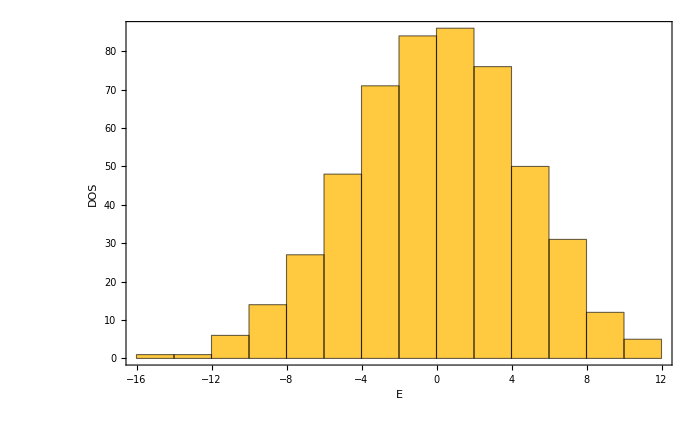

```mathematica
Histogram[evals,sharedPlotOptions,FrameLabel->{"E","DOS"}]
```

```mathematica
newevals=Unfold[evals];
```

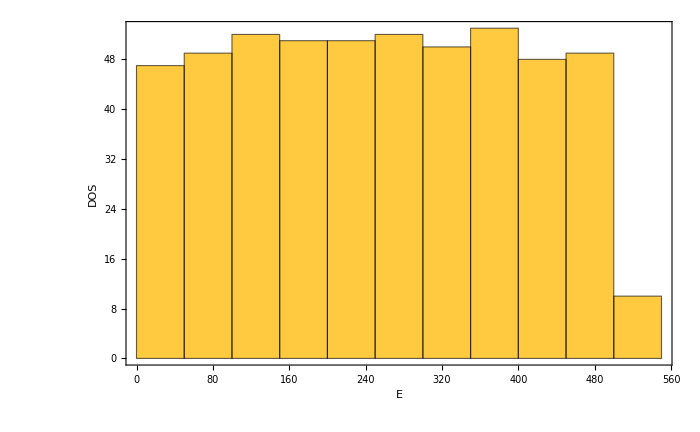

```mathematica
Histogram[newevals["UnfoldedLevels"],sharedPlotOptions,FrameLabel->{"E","DOS"}]
```

```mathematica
tList=Range[0,d,0.5];
ensembleSize=50;

texturesEnsemble=Table[
H=IsingHamiltonian[hx+RandomReal[{-0.05,0.05}],hz+RandomReal[{-0.05,0.05}],J,L]+h1*Pauli[{3}~Join~ConstantArray[0,L-1]]+hL*Pauli[ConstantArray[0,L-1]~Join~{3}];
texture=QuantumTexture[Normal[H]];
texture[tList]
,ensembleSize];
```

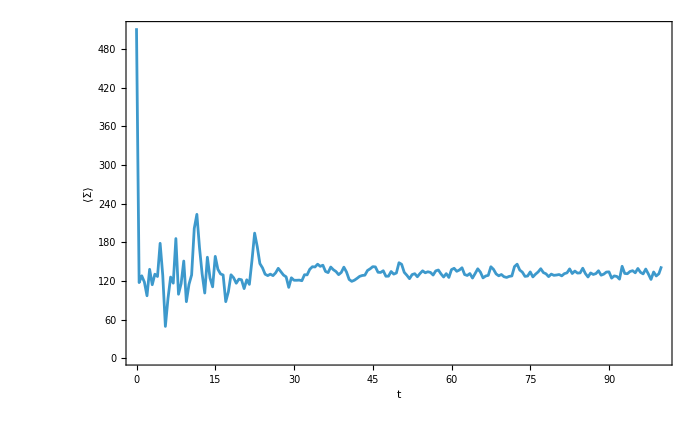

```mathematica
ListPlot[Transpose[{tList,Mean[texturesEnsemble]}],
Joined->True,
PlotRange->All,
sharedPlotOptions,
FrameLabel->{"t", "⟨Σ⟩"}
]
```

## SFF

```mathematica
L=10;
J=1.;
hx=1.05;
hz=0.5;
h1=0.25;
hL=-0.25;
H=IsingHamiltonian[hx,hz,J,L]+h1*Pauli[{3}~Join~ConstantArray[0,L-1]]+hL*Pauli[ConstantArray[0,L-1]~Join~{3}];
```

```mathematica
evals=Eigenvalues[Normal[H]];
```

```mathematica
newevals=Unfold[evals];
```

```mathematica
(* Parameters *)
tauMax = 1000;
dtau = 0.1;
tauList = Range[0, tauMax, dtau];
windowSize = 200; (* moving average window, adjust later *)
```

```mathematica
(* Compute Z(tau) *)
Z[tau_] := Total[Exp[-I * newevals["UnfoldedLevels"] * tau]];
Zvals=Exp[-I*Outer[Times,newevals["UnfoldedLevels"],tauList]]//Total;

(* Raw SFF *)
Kraw = Abs[Zvals]^2;

(* Disconnected part via moving average *)
halfW = Floor[windowSize/2];
Zdisconn = Table[
  Mean[Zvals[[Max[1,i-halfW] ;; Min[Length[Zvals],i+halfW]]]],
  {i, 1, Length[Zvals]}
];
Kdisc = Abs[Zdisconn]^2;

(* Connected SFF *)
Kconn = Kraw - Kdisc;
```

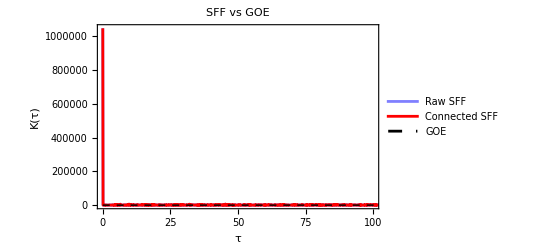

```mathematica
nLevels=Length[newevals["UnfoldedLevels"]]; (* =1024 for L=10*)
tH=nLevels; (*Heisenberg time in unfolded units*)

(*GOE analytical connected SFF,normalized by N*)
tNorm=tauList/tH;
Kgoe=tH*Table[If[t<=1,2t-t*Log[1+2t],2-t*Log[(2t+1)/(2t-1)]],{t,tNorm}];

(*Plot*)
ListLinePlot[{Transpose[{tauList,Kraw}],Transpose[{tauList,Kconn}],Transpose[{tauList,Kgoe}]},PlotLegends->{"Raw SFF","Connected SFF","GOE"},PlotStyle->{Directive[Blue,Opacity[0.5]],Red,Directive[Black,Thick,Dashed]},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"SFF vs GOE",PlotRange->{{0,100},All}]
```

## Ensemble

```mathematica
(* ── Compiled SFF kernel ─────────────────────────────────── *)
CompileSFFcomplex = Compile[{{spec, _Real, 1}, {taus, _Real, 1}},
  Table[Total[Cos[2. Pi spec t]] + I Total[Sin[2. Pi spec t]], {t, taus}],
  CompilationTarget -> "WVM", RuntimeOptions -> "Speed"];
```

```mathematica
(* ── Parameters ─────────────────────────────────────────── *)
L = 10; J = 1.; hx = 1.05; hz = 0.5; h1 = 0.25; hL = -0.25;
trimFraction = 0.1;
Nensemble = 50;
SeedRandom[41];
hzList = RandomReal[{hz*0.99, hz*1.01}, Nensemble];
```

```mathematica
(* ── Parameters ─────────────────────────────────────────── *)
L = 10; J = 1.; hx = 1.1; hz = 0.35; h1 = 0.25; hL = -0.25;
trimFraction = 0.1;
Nensemble = 50;
SeedRandom[41];
hzList = RandomReal[{hz*0.99, hz*1.01}, Nensemble];
```

```mathematica
(* ── Build ensemble: diagonalize, unfold, trim, rescale ──── *)
ensembleUnfolded = Table[
  ev = Sort @ Eigenvalues @ Normal[
    IsingHamiltonian[hx, hzVal, J, L] +
    h1*Pauli[{3}~Join~ConstantArray[0, L-1]] +
    hL*Pauli[ConstantArray[0, L-1]~Join~{3}]];
  unf = Unfold[ev]["UnfoldedLevels"];
  nTrim = Floor[trimFraction * Length[unf]];
  unf = unf[[nTrim + 1 ;; -nTrim - 1]];
  unf / Mean[Differences[unf]]   (* unit mean spacing *)
  , {hzVal, hzList}];

nLevels = Length[ensembleUnfolded[[1]]];
```

```mathematica
(* ── τ grid (Heisenberg units) ───────────────────────────── *)
tauMax = 3.; nPts = 2000;
tauList = N[Range[1, nPts] (tauMax/nPts)];
(* ── GOE analytical (Heisenberg units) ───────────────────── *)
Kgoe = If[# == 0, 0,
  If[# <= 1, 2# - # Log[1 + 2#], 2 - # Log[(2#+1)/(2#-1)]]] & /@ tauList;
```

```mathematica
(* ── SFF ─────────────────────────────────────────────────── *)
Zvals = CompileSFFcomplex[#, tauList] & /@ ensembleUnfolded;
Kraw  = Mean[Abs[Zvals]^2] / nLevels;
Kdisc = Abs[Mean[Zvals]]^2 / nLevels;
Kconn = Kraw - Kdisc;
```

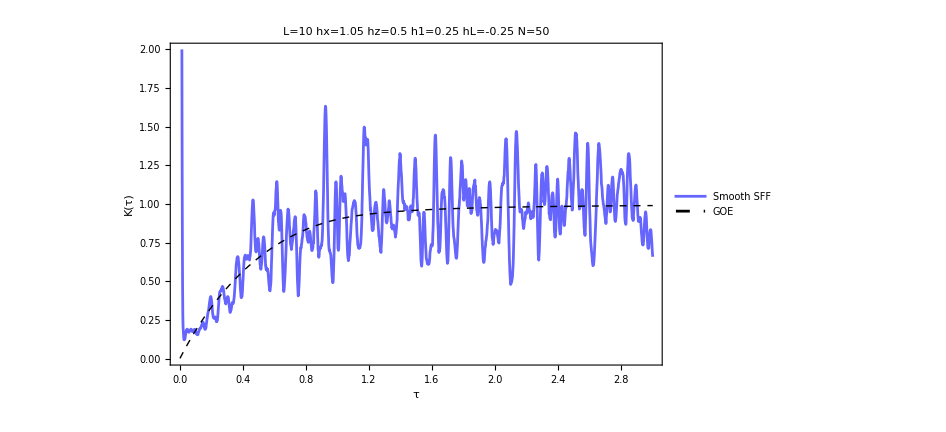

```mathematica
ListLinePlot[{Transpose[{tauList,GaussianFilter[Kraw,10]}],Transpose[{tauList,Kgoe}]},PlotLegends->{"Smooth SFF","GOE"},PlotStyle->{Directive[Blue,Opacity[0.6]],Directive[Black,Thick,Dashed]},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->Row[{"L=",L,"  hx=",hx,"  hz=",hz,"  h1=",h1,"  hL=",hL,"  N=",Nensemble}],PlotRange->{{0,tauMax},{0,2}},FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ImageSize->700]
```

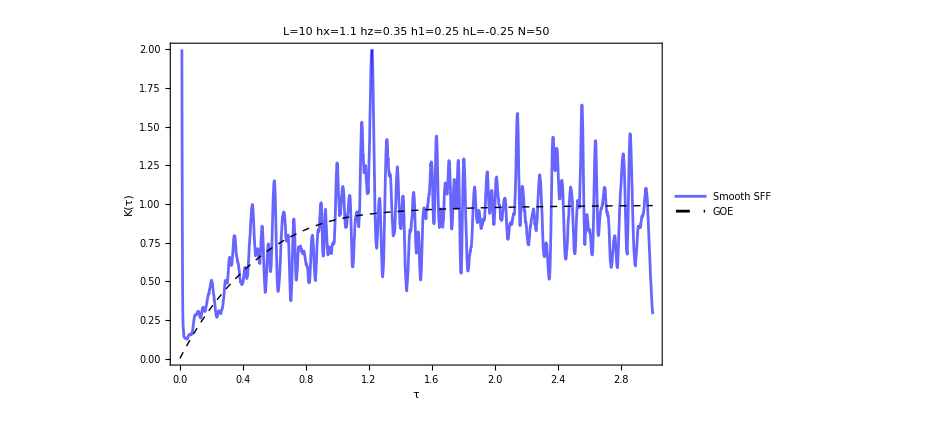

```mathematica
ListLinePlot[{Transpose[{tauList,GaussianFilter[Kraw,10]}],Transpose[{tauList,Kgoe}]},PlotLegends->{"Smooth SFF","GOE"},PlotStyle->{Directive[Blue,Opacity[0.6]],Directive[Black,Thick,Dashed]},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->Row[{"L=",L,"  hx=",hx,"  hz=",hz,"  h1=",h1,"  hL=",hL,"  N=",Nensemble}],PlotRange->{{0,tauMax},{0,2}},FrameStyle->Directive[Black,18],LabelStyle->Directive[Black,18],ImageSize->700]
```

# Kicked ising

```mathematica
Off[MakeExpression::boxfmt]

(* ============================================================ *)
(*  Mixed-Field Ising Model — Floquet texture test               *)
(* ============================================================ *)

L  = 8;            (* number of spins, dim = 2^L = 1024 *)
J  = 1.0;
hz = 0.8090;        (* Kim-Huse chaotic parameters *)
hx = 0.9045;
tau = 1.0;
dim = 2^L;
```

```mathematica
(* Pauli matrices *)
Id2 = IdentityMatrix[2];
sx  = {{0, 1}, {1, 0}};
sz  = {{1, 0}, {0, -1}};

(* Single-site operator embedded in the L-site space *)
op[mat_, i_, len_] := 
  KroneckerProduct @@ Table[If[k == i, mat, Id2], {k, 1, len}];

(* Diagonal part: Ising + longitudinal field, open BC *)
Hz = -J Sum[op[sz, i, L] . op[sz, i + 1, L], {i, 1, L - 1}]- hz Sum[op[sz, i, L], {i, 1, L}];

(* Off-diagonal part: transverse field *)
Hx = -hx Sum[op[sx, i, L], {i, 1, L}];
```

```mathematica
diagHz   = Normal[Diagonal[Hz]];
expHz    = DiagonalMatrix[Exp[-I tau diagHz]];
sqrtHz   = DiagonalMatrix[Exp[-I tau diagHz/2]];
expHx    = MatrixExp[-I tau Hx];

UF    = expHz . expHx;
UFsym = sqrtHz . expHx . sqrtHz;
```

```mathematica
{eval1, vec1} = Eigensystem[UF];
{eval2, vec2} = Eigensystem[UFsym];
```

```mathematica
vec1[[1]][[1;;-1;;50]]//Im//Chop
```

{0,-0.00632292,-0.108334,0,0.0184299,0.0142525}

```mathematica
vec2[[1]][[1;;-1;;50]]//Im//Chop
```

{0,0,0,0,0,0}

```mathematica
f1 = ConstantArray[1./Sqrt[dim], dim];

P1 = Abs[vec1 . f1]^2;
P2 = Abs[vec2 . f1]^2;

sat1 = dim * Total[P1^2];
sat2 = dim * Total[P2^2];
```

```mathematica
Print["Asymmetric U_F  :  Σ∞ = ", sat1, "   (expect ~2, CUE-like)"];
Print["Symmetric U_F   :  Σ∞ = ", sat2, "   (expect ~3, COE)"];

(* Optional sanity check: maximum imaginary component of UFsym eigenvectors *)
Print["max |Im(vec_sym)| = ", Max[Abs[Im[vec2]]],
      "   (should be ~ machine epsilon up to a global phase)"];
```

Asymmetric U_F  :  Σ∞ = 6.61063   (expect ~2, CUE-like)

Symmetric U_F   :  Σ∞ = 6.30865   (expect ~3, COE)

max |Im(vec_sym)| = 8.31626×10^-14   (should be ~ machine epsilon up to a global phase)

## Change of basis

```mathematica
gaugeSweep[theta_] := Module[{D, U, V, P},
  D = DiagonalMatrix[Exp[-I theta diagHz]];
  U = D . UFsym . ConjugateTranspose[D];
  V = Eigenvectors[U];
  P = Abs[V . f1]^2;
  dim * Total[P^2]
];
```

```mathematica
sweep = Table[{theta, gaugeSweep[theta]}, {theta, 0, tau/2, tau/40}];
```

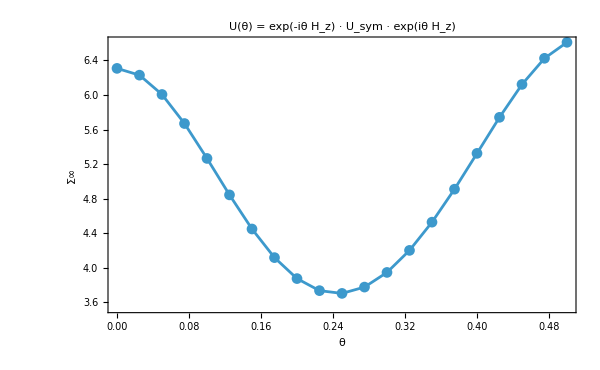

```mathematica
ListLinePlot[sweep,
  PlotMarkers -> Automatic,
  Frame -> True,
  FrameLabel -> {"θ", "Σ∞"},
  GridLines -> {None, {2, 3}},
  PlotRange -> All,
  PlotLabel -> "U(θ) = exp(-iθ H_z) · U_sym · exp(iθ H_z)",
  ImageSize -> 600
]
```

```mathematica
sweep
```

{{0.,6.30865},{0.025,6.23016},{0.05,6.00644},{0.075,5.66978},{0.1,5.26565},{0.125,4.8434},{0.15,4.44837},{0.175,4.11684},{0.2,3.87403},{0.225,3.73431},{0.25,3.70245},{0.275,3.77557},{0.3,3.94543},{0.325,4.2006},{0.35,4.5275},{0.375,4.90947},{0.4,5.3243},{0.425,5.74163},{0.45,6.12286},{0.475,6.42532},{0.5,6.61063}}

## Entanglement

```mathematica
EntanglementEntropySVD[psi_, dA_, dB_] :=
  Module[{mat, sv2},
    mat = ArrayReshape[psi, {dA, dB}];
    sv2 = SingularValueList[mat]^2;
    (* Hard threshold at machine epsilon level *)
    sv2 = Select[sv2, # > 1.*^-14 &];
    (* Renormalize to absorb discarded numerical noise *)
    sv2 = sv2 / Total[sv2];
    -sv2 . Log[sv2]
  ]
```

```mathematica
entanglement=ParallelTable[EntanglementEntropySVD[i, L/2,L/2 ],{i,vec1}];
```

```mathematica
entanglement2=ParallelTable[EntanglementEntropySVD[i, L/2,L/2 ],{i,vec2}];
```

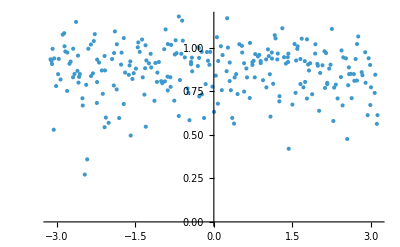

```mathematica
ListPlot[Transpose[{Arg[eval1],entanglement}],PlotRange->All]
```

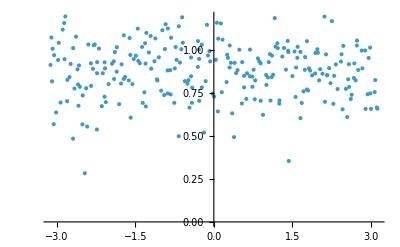

```mathematica
ListPlot[Transpose[{Arg[eval2],entanglement2}],PlotRange->All]
```

```mathematica
PageEntropy[La_,Lb_]:=N[PolyGamma[0,2^La*2^Lb+1]-PolyGamma[0,2^Lb+1]-(2^La-1)/(2*2^Lb)]
```

```mathematica
La=4;
Lb=4;
```

```mathematica
PageEntropy[La,Lb]//N
```

2.27487

```mathematica
Print["dA, dB = ",{2^La,2^Lb}];
Print["Max possible entropy = ",N[Log[Min[2^La,2^Lb]]]];
Print["Page value = ",PageEntropy[La,Lb]];
```

dA, dB = {16,16}

Max possible entropy = 2.77259

Page value = 2.27487

```mathematica
Print["Mean Schmidt rank: ",Mean[Length[Select[SingularValueList[ArrayReshape[#,{2^La,2^Lb}]]^2,#>10^-14&]]&/@vec1]];
```

Mean Schmidt rank: 16

```mathematica
phases=Mod[Arg[eval1],2 Pi];
spacings=Differences[Sort[phases]];
ratios=Min[#1/#2,#2/#1]&@@@Partition[spacings,2,1];
Mean[ratios]
```

0.416354

```mathematica
{J,hz,hx,tau} (*print these to verify*)
```

{1.,0.809,0.9045,1.}

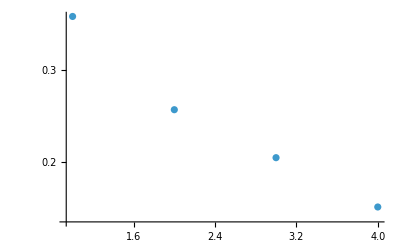

```mathematica
sv=SingularValueList[ArrayReshape[vec1[[1]],{64,64}]];
ListLogPlot[sv^2,PlotRange->All]
```